## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

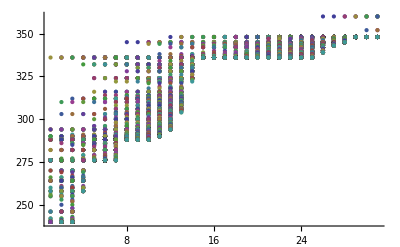

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

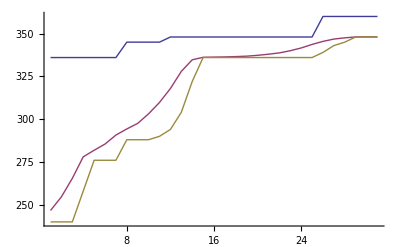

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

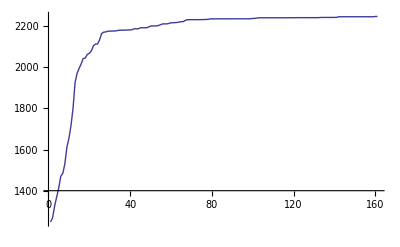

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

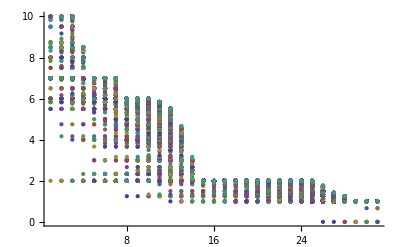

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

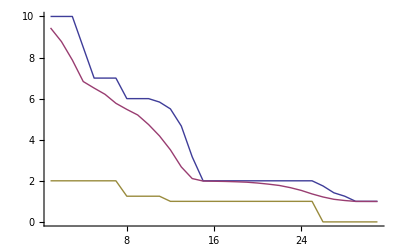

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

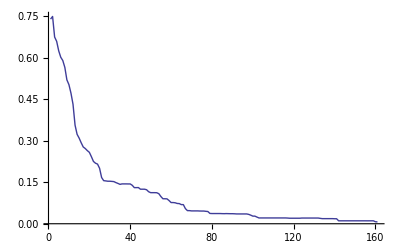

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

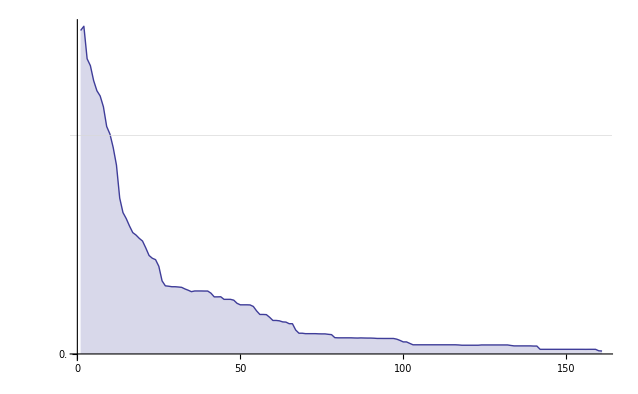

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

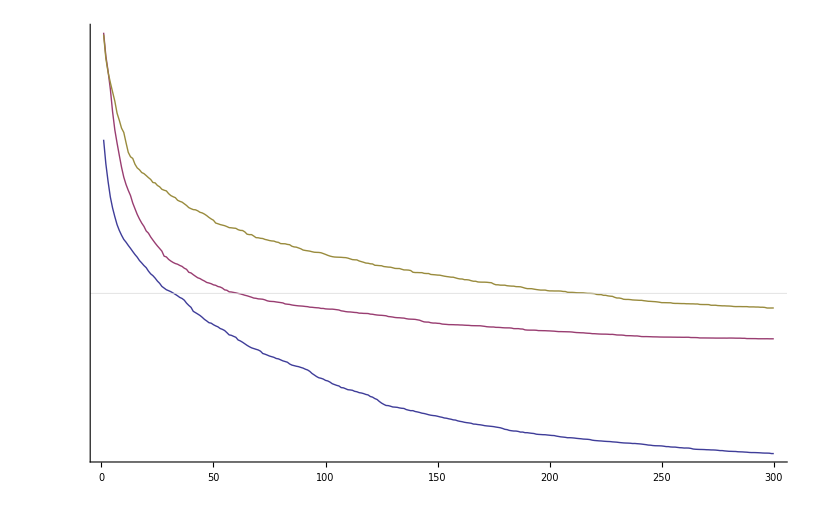

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

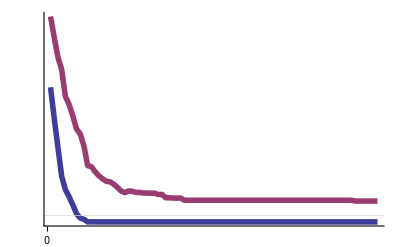

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

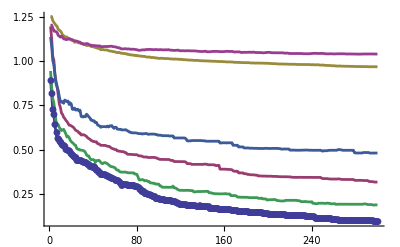

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

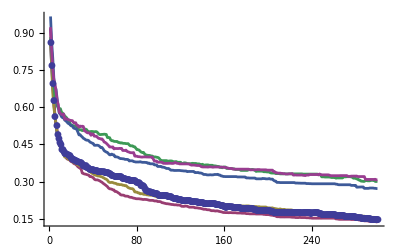

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

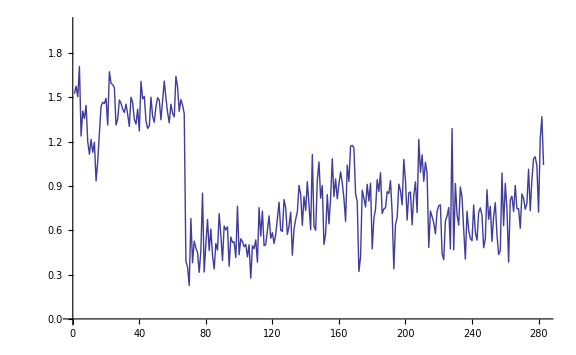

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

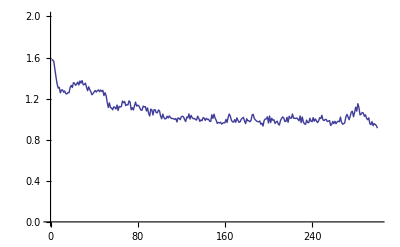

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

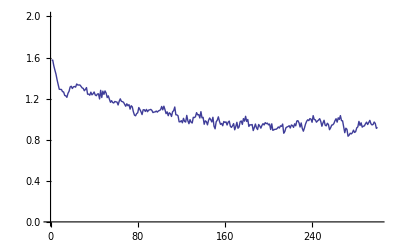

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

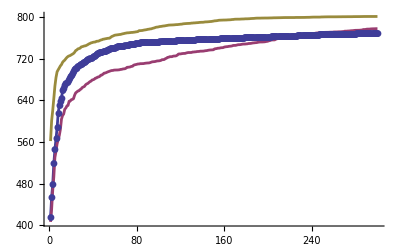

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

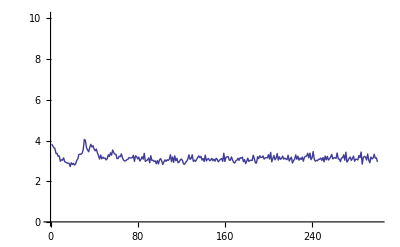

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

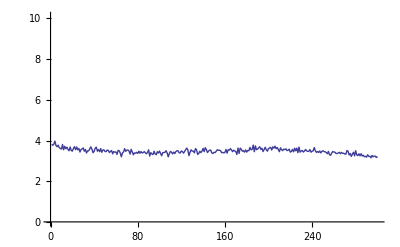

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

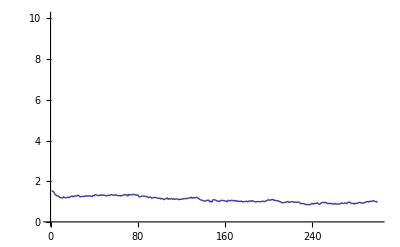

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

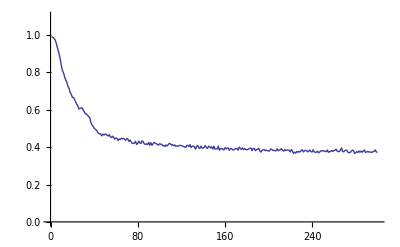

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

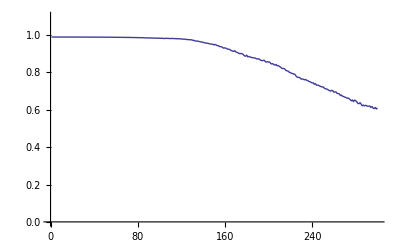

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

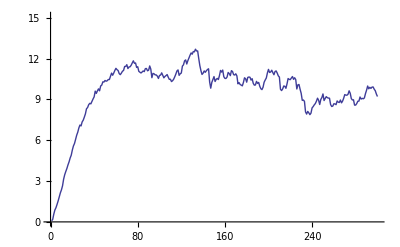

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```